Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Set::ssym: Removed[alphaH] is not a symbol.

Set::ssym: Removed[alphaM] is not a symbol.

Set::ssym: Removed[cH] is not a symbol.

General::stop: Further output of Set::ssym will be suppressed during this calculation.

Precomputing No-RIS local-basis polynomial data...

Computing analytical CF curves...

Computing streaming MC markers, memory-safe and silent...

Done. SOP RIS vs No-RIS comparison files saved in: C:\Users\Mahin1\Documents

Max absolute CF-MC error = 0.00378

Publication figure exported as PNG/PDF/SVG: C:\Users\Mahin1\Documents\SOP_RIS_vs_NoRIS_ZIS_TUNABLE_COMPARISON.png

Publication-quality vector figure preview:

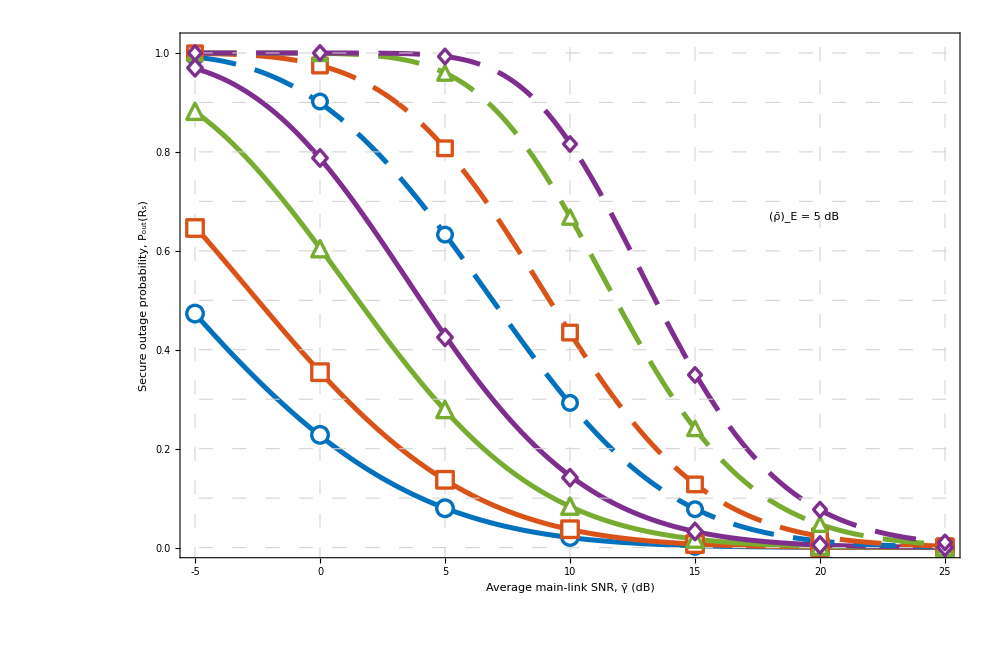

```mathematica
(* ::Package::*)(*SOP_RIS_vs_NoRIS_ZIS_TUNABLE_COMPARISON.wl Final comparison graph for SOP:RIS vs No-RIS,single legitimate user,strongest eavesdropper with Ne={1,2,6,15}.Locked cores used:-No-RIS SOP core:optimized ZIS piecewise closed-form with local scaled basis t=(x-xC)/xS,incomplete-gamma moments,MC comparison fixed with Thread[].-RIS SOP core:non-integer ZIS piecewise closed-form in stable RIS Gamma-domain u=Sqrt[gammaD/betaD],incomplete-gamma moments,MC validation.Analytical-curve rules:-no NIntegrate-no NSum-no quadrature kernel-no Monte Carlo in analytical curve-MC markers only for validation Output:Saves PNG/PDF/CSV in the same folder as this.wl file.Shows a light raster preview in the notebook to avoid Mathematica frontend crashes.Run:Double-click this file,then press Shift+Enter.*)$HistoryLength=0;
Quiet[CloseKernels[]];
ClearSystemCache[];
Quiet[Remove["Global`*"]];

(* ============================================================*)
(*1) MASTER PARAMETER PANEL-EDIT ONLY THIS BLOCK FIRST*)
(* ============================================================*)

(*----------------OUTPUT/RUNTIME----------------*)
codeDir=Module[{d},d=Quiet@Check[DirectoryName[$InputFileName],$Failed];
If[StringQ[d]&&d=!=""&&DirectoryQ[d],d,d=Quiet@Check[NotebookDirectory[],$Failed];
If[StringQ[d]&&d=!=""&&DirectoryQ[d],d,Directory[]]]];
SetDirectory[codeDir];

baseName="SOP_RIS_vs_NoRIS_ZIS_TUNABLE_COMPARISON";
autoOpenFolder=True;
showRasterPreviewInNotebook=False;
showVectorFigureInNotebook=True;
useParallelAnalytical=True;
requestedKernels=8;

(*----------------MAIN CURVE/AXIS SETTINGS----------------*)
NeList={1,2,6,15};

Rs=0.5;                         (*Higher Rs->all curves move right/up;lower Rs->left/down*)
rhoEveDB=5;                     (*Higher Eve SNR->all curves right/up;lower->left/down*)
rhoMainDBList=Range[-5,25,1];  (*Analytical curve x-axis points*)
rhoMainDBMC=Range[-5,25,5];    (*MC marker x-axis points*)

(*----------------DIRECT VISUAL SHIFT CONTROLS---------------- Main-link physical shifts:+dB makes that method look stronger->curve moves left/down.-dB makes that method look weaker->curve moves right/up.Eavesdropper physical shifts:+dB makes Eve stronger->curve moves right/up.-dB makes Eve weaker->curve moves left/down.Use these four first when you only need visual separation/alignment.*)
rhoRISPhysicalShiftDB=0;
rhoNoRISPhysicalShiftDB=0;
rhoEveRISPhysicalShiftDB=0;
rhoEveNoRISPhysicalShiftDB=0;

(*----------------NO-RIS CHANNEL/APPROXIMATION SETTINGS----------------*)
alphaM=8/5;       (*Main-link generalized-gamma alpha.Bigger can sharpen/shift No-RIS curve.*)
cM=5/2;       (*Main-link generalized-gamma shape.Bigger usually improves No-RIS reliability.*)
alphaH=3/2;       (*Eve-link generalized-gamma alpha.*)
cH=3/2;       (*Eve-link generalized-gamma shape.Bigger usually worsens SOP if Eve is stronger.*)

polyDegNoRIS=14;  (*Accuracy/smoothness of No-RIS local polynomial;increase if curve wiggles.*)
yBreaksNoRIS={0,0.02,0.05,0.1,0.2,0.5,1,2,4,8,16,32,50,80};
wpNoRIS=80;

(*----------------RIS CHANNEL/APPROXIMATION SETTINGS----------------*)
lambdaD=4;     (*Destination square-root-Gamma shape.Bigger->RIS usually stronger/left.*)
lambdaE=1.3;    (*Eve square-root-Gamma shape.Bigger->Eve usually stronger/right.*)
muD=1.8;     (*RIS destination scale multiplier.Bigger->RIS left/down.*)
muE=0.5;     (*RIS Eve scale multiplier.Bigger->RIS right/up.*)

polyDegRIS=2;     (*RIS local polynomial degree;2 is stable.Increase carefully.*)
uStepRIS=0.05;    (*Smaller->smoother/more accurate but slower.*)
uBaseTailRIS=18.0;
uSafetyRIS=12.0;
minIntervalsRIS=40;
wpRIS=60;

(*----------------MONTE CARLO MARKER SETTINGS----------------*)
mcSamplesPerMarker=80000;   (*Increase only after final plot shape is acceptable.*)
mcBatchSize=5000;
mcSeedBase=24681357;

(*----------------PUBLICATION FIGURE SETTINGS---------------- This block completely replaces the previous tiny/default plot layer.Computation is unchanged.These are only Q1-ready graphics controls.*)

(*Color-blind-safe,high-contrast palette.Same color means same Ne across RIS/No-RIS.*)
colors={RGBColor[0.000,0.447,0.741],RGBColor[0.850,0.325,0.098],RGBColor[0.466,0.674,0.188],RGBColor[0.494,0.184,0.556]};
shapeNames={"circle","square","triangle","diamond"};

(*Curve style:RIS solid,No-RIS dashed.*)
lineThicknessRIS=AbsoluteThickness[3.6];
lineThicknessNoRIS=AbsoluteThickness[3.6];
noRISLineStyle=Dashing[{0.030,0.014}];
plotInterpolationOrder=2;

(*IMPORTANT:Mathematica PlotMarkers uses point-size numbers.Do not use 0.01.*)
markerSizeRIS=17;
markerSizeNoRIS=15;
markerEdgeThickness=AbsoluteThickness[2.4];

(*Notebook/export size.Direct vector preview is now shown in the notebook.*)
showRasterPreviewInNotebook=False;
showVectorFigureInNotebook=True;
plotImageSize=1000;
exportResolutionDPI=450;

(*Axes,frame,fonts,layout.*)
plotYRange={0,1.02};
plotXRange={Min[rhoMainDBList],Max[rhoMainDBList]};
plotGridLines={Range[Min[rhoMainDBList],Max[rhoMainDBList],5],Range[0,1,0.1]};
plotAspectRatio=0.66;
frameThickness=AbsoluteThickness[1.65];
majorTickLength=0.018;
minorTickLength=0.010;
baseFontSize=19;
labelFontSize=22;
tickFontSize=18;
legendFontSize=15;
titleFontSize=22;
legendPosition={0.80,0.65};
legendBackgroundOpacity=0.88;

xAxisLabel="Average main-link SNR, \!\(\*OverscriptBox[\(γ\), \(_\)]\) (dB)";
yAxisLabel="Secure outage probability, \!\(\*SubscriptBox[\(P\), \(out\)]\)(\!\(\*SubscriptBox[\(R\), \(s\)]\))";

(* ============================================================*)
(*2) RUNTIME INITIALIZATION+MARKER HELPERS*)
(* ============================================================*)

If[useParallelAnalytical,Quiet[CloseKernels[]];
LaunchKernels[Min[requestedKernels,$ProcessorCount]];
ParallelEvaluate[$HistoryLength=0;];];

markerGraphics[color_,shape_]:=Switch[shape,"circle",Graphics[{EdgeForm[{color,markerEdgeThickness}],FaceForm[White],Disk[]}],"square",Graphics[{EdgeForm[{color,markerEdgeThickness}],FaceForm[White],Rectangle[{-1,-1},{1,1}]}],"triangle",Graphics[{EdgeForm[{color,markerEdgeThickness}],FaceForm[White],Polygon[{{0,1.13},{-1.08,-1},{1.08,-1}}]}],"diamond",Graphics[{EdgeForm[{color,markerEdgeThickness}],FaceForm[White],Polygon[{{0,1.22},{1.08,0},{0,-1.22},{-1.08,0}}]}]];
markers=Table[markerGraphics[colors[[i]],shapeNames[[i]]],{i,Length[NeList]}];

(* ============================================================*)
(*3) COMMON HELPERS/DERIVED SOP THRESHOLDS*)
(* ============================================================*)

dB2lin[x_?NumericQ]:=10^(x/10);
clip01[x_?NumericQ]:=If[x<0,0.,If[x>1,1.,N[x]]];

lowerRegGamma[a_,z_]:=GammaRegularized[a,0,z];
upperRegGamma[a_,z_]:=GammaRegularized[a,z];

tau=Exp[2 Rs];
aSOP=tau-1;
bSOP=tau;

(* ============================================================*)
(*4) NO-RIS SOP CORE-PARAMETERS ARE IN MASTER PANEL*)
(* ============================================================*)

nuM=alphaM/2;
nuH=alphaH/2;
rhoEbarNoRIS=dB2lin[rhoEveDB+rhoEveNoRISPhysicalShiftDB];
xBreaksNoRIS=aSOP+bSOP*yBreaksNoRIS;
xTailNoRIS=Last[xBreaksNoRIS];

noRISggCDF[x_?NumericQ,alpha_?NumericQ,c_?NumericQ,gbar_?NumericQ]:=If[x<=0,0.,N[GammaRegularized[c,0,(x/gbar)^(alpha/2)]]];

noRISMomentInterval[n_Integer?NonNegative,xL_?NumericQ,xU_?NumericQ,rhoMbar_?NumericQ]:=Module[{xiM,Bm,shape,zL,zU},xiM=SetPrecision[rhoMbar^(-nuM),wpNoRIS];
Bm=SetPrecision[nuM/(Gamma[cM] rhoMbar^(nuM*cM)),wpNoRIS];
shape=SetPrecision[(n+nuM*cM)/nuM,wpNoRIS];
zL=SetPrecision[xiM*xL^nuM,wpNoRIS];
zU=SetPrecision[xiM*xU^nuM,wpNoRIS];
N[Bm*(1/nuM)*xiM^(-shape)*(Gamma[shape,0,zU]-Gamma[shape,0,zL]),40]];

noRISLocalMomentInterval[j_Integer?NonNegative,xL_?NumericQ,xU_?NumericQ,xC_?NumericQ,xS_?NumericQ,rhoMbar_?NumericQ]:=Module[{val},val=Sum[Binomial[j,r]*(-xC)^(j-r)/xS^j*noRISMomentInterval[r,xL,xU,rhoMbar],{r,0,j}];
Re[N[val,40]]];

noRISDestTailCCDF[rhoMbar_?NumericQ]:=N[GammaRegularized[cM,(xTailNoRIS/rhoMbar)^nuM],40];

buildNoRISPolyData[Ne_Integer?Positive]:=buildNoRISPolyData[Ne]=Module[{hFun,polyCoeffData},hFun[x_?NumericQ]:=Module[{y},y=(x-aSOP)/bSOP;
If[y<=0,0.,noRISggCDF[y,alphaH,cH,rhoEbarNoRIS]^Ne]];
polyCoeffData=Table[Module[{xL,xU,xC,xS,nodes,tnodes,values,tt,poly,coeffs},xL=SetPrecision[xBreaksNoRIS[[i]],wpNoRIS];
xU=SetPrecision[xBreaksNoRIS[[i+1]],wpNoRIS];
xC=SetPrecision[(xL+xU)/2,wpNoRIS];
xS=SetPrecision[(xU-xL)/2,wpNoRIS];
nodes=Table[xC+xS*Cos[((2*j-1)*Pi)/(2*(polyDegNoRIS+1))],{j,1,polyDegNoRIS+1}];
tnodes=SetPrecision[(nodes-xC)/xS,wpNoRIS];
values=SetPrecision[hFun/@N[nodes,50],wpNoRIS];
poly=InterpolatingPolynomial[Thread[{tnodes,values}],tt];
coeffs=CoefficientList[Expand[poly],tt];
{xL,xU,xC,xS,coeffs}],{i,1,Length[xBreaksNoRIS]-1}];
<|"Ne"->Ne,"PolyCoeffData"->polyCoeffData|>];

noRISSOPZISAnalytical[rhoMbarDB_?NumericQ,Ne_Integer?Positive]:=Module[{rhoMbar,pdata,sumLow,sumTail,xL,xU,xC,xS,coeffs,intervalSum,pno},rhoMbar=dB2lin[rhoMbarDB+rhoNoRISPhysicalShiftDB];
pdata=buildNoRISPolyData[Ne];
sumLow=Sum[xL=pdata["PolyCoeffData"][[i,1]];
xU=pdata["PolyCoeffData"][[i,2]];
xC=pdata["PolyCoeffData"][[i,3]];
xS=pdata["PolyCoeffData"][[i,4]];
coeffs=pdata["PolyCoeffData"][[i,5]];
intervalSum=Sum[coeffs[[n+1]]*noRISLocalMomentInterval[n,xL,xU,xC,xS,rhoMbar],{n,0,Length[coeffs]-1}];
intervalSum,{i,1,Length[pdata["PolyCoeffData"]]}];
sumTail=noRISDestTailCCDF[rhoMbar];
pno=Re[N[sumLow+sumTail,30]];
clip01[1-pno]];

noRISSOPMC[rhoMbarDB_?NumericQ,Ne_Integer?Positive,nsamp_Integer?Positive,seed_Integer]:=Module[{rhoMbar,remaining,batch,totalBad,zD,zE,gammaM,gammaEMax,thr},BlockRandom[SeedRandom[seed];
rhoMbar=dB2lin[rhoMbarDB+rhoNoRISPhysicalShiftDB];
remaining=nsamp;
totalBad=0;
While[remaining>0,batch=Min[mcBatchSize,remaining];
zD=RandomVariate[GammaDistribution[N[cM],1],batch];
gammaM=rhoMbar*(zD^(2/N[alphaM]));
zE=RandomVariate[GammaDistribution[N[cH],1],{batch,Ne}];
gammaEMax=Max/@(rhoEbarNoRIS*(zE^(2/N[alphaH])));
thr=tau*(1+gammaEMax)-1;
totalBad+=Total[Boole[Thread[gammaM<thr]]];
remaining-=batch;
Clear[zD,zE,gammaM,gammaEMax,thr];];
N[totalBad/nsamp]]];

(* ============================================================*)
(*5) RIS SOP CORE-PARAMETERS ARE IN MASTER PANEL*)
(* ============================================================*)

rhoEbarRIS=dB2lin[rhoEveDB+rhoEveRISPhysicalShiftDB];

risEveCDF[y_?NumericQ,betaE_?NumericQ]:=Module[{arg},If[y<=0,0.0,arg=Sqrt[y/betaE];
N[GammaRegularized[lambdaE,0,arg]]]];

risUMoment[k_Integer?NonNegative,u1_?NumericQ,u2_?NumericQ]:=Module[{aa},aa=lambdaD+k;
N[(Gamma[aa]/Gamma[lambdaD])*(GammaRegularized[aa,0,u2]-GammaRegularized[aa,0,u1]),40]];

risLocalUMoment[j_Integer?NonNegative,uL_?NumericQ,uU_?NumericQ,uC_?NumericQ,uS_?NumericQ]:=Module[{val},val=Sum[Binomial[j,r]*(-uC)^(j-r)/uS^j*risUMoment[r,uL,uU],{r,0,j}];
Re[N[val,40]]];

chebNodes[lo_?NumericQ,hi_?NumericQ,deg_Integer?NonNegative]:=Module[{mid,rad},mid=(lo+hi)/2;rad=(hi-lo)/2;
Sort[Table[mid+rad*Cos[(2*j-1)*Pi/(2*(deg+1))],{j,1,deg+1}]]];

risSOPZISAnalytical[gammaDbarDB_?NumericQ,Ne_Integer?Positive]:=Module[{gammaDbar,betaD,betaE,u0,uTail,nInt,grid,hFun,sumPart,tailPart,lo,hi,uC,uS,nodes,snodes,vals,ss,poly,coeffs,contrib,pno},gammaDbar=dB2lin[gammaDbarDB+rhoRISPhysicalShiftDB];
betaD=gammaDbar*muD;
betaE=rhoEbarRIS*muE;
u0=Sqrt[aSOP/betaD];
uTail=Max[uBaseTailRIS,u0+uSafetyRIS];
nInt=Max[minIntervalsRIS,Ceiling[(uTail-u0)/uStepRIS]];
grid=N[Subdivide[u0,uTail,nInt],30];
hFun[u_?NumericQ]:=Module[{x,y},x=betaD*u^2;
y=(x-aSOP)/bSOP;
If[y<=0,0.0,N[risEveCDF[y,betaE]^Ne]]];
sumPart=Sum[lo=grid[[i]];hi=grid[[i+1]];
uC=(lo+hi)/2;uS=(hi-lo)/2;
nodes=chebNodes[lo,hi,polyDegRIS];
snodes=N[(nodes-uC)/uS,40];
vals=SetPrecision[hFun/@nodes,wpRIS];
poly=InterpolatingPolynomial[Thread[{snodes,vals}],ss];
coeffs=CoefficientList[Expand[poly],ss];
contrib=Sum[coeffs[[n+1]]*risLocalUMoment[n,lo,hi,uC,uS],{n,0,Length[coeffs]-1}];
contrib,{i,1,Length[grid]-1}];
tailPart=N[GammaRegularized[lambdaD,uTail],40];
pno=Re[N[sumPart+tailPart,30]];
clip01[1-pno]];

risSOPMC[gammaDbarDB_?NumericQ,Ne_Integer?Positive,nsamp_Integer?Positive,seed_Integer]:=Module[{gammaDbar,betaD,betaE,remaining,batch,totalBad,uD,uE,gammaD,gammaEMax,thr},BlockRandom[SeedRandom[seed];
gammaDbar=dB2lin[gammaDbarDB+rhoRISPhysicalShiftDB];
betaD=gammaDbar*muD;
betaE=rhoEbarRIS*muE;
remaining=nsamp;
totalBad=0;
While[remaining>0,batch=Min[mcBatchSize,remaining];
uD=RandomVariate[GammaDistribution[N[lambdaD],1],batch];
gammaD=betaD*uD^2;
uE=RandomVariate[GammaDistribution[N[lambdaE],1],{batch,Ne}];
gammaEMax=Max/@(betaE*(uE^2));
thr=tau*(1+gammaEMax)-1;
totalBad+=Total[Boole[Thread[gammaD<thr]]];
remaining-=batch;
Clear[uD,uE,gammaD,gammaEMax,thr];];
N[totalBad/nsamp]]];

(* ============================================================*)
(*6) DATA GENERATION*)
(* ============================================================*)

Print["Precomputing No-RIS local-basis polynomial data..."];
Do[buildNoRISPolyData[Ne],{Ne,NeList}];

Print["Computing analytical CF curves..."];
cfRowsRIS=If[useParallelAnalytical,Flatten[ParallelTable[{"RIS",Ne,rhoDB,risSOPZISAnalytical[rhoDB,Ne]},{Ne,NeList},{rhoDB,rhoMainDBList}],1],Flatten[Table[{"RIS",Ne,rhoDB,risSOPZISAnalytical[rhoDB,Ne]},{Ne,NeList},{rhoDB,rhoMainDBList}],1]];
cfRowsNoRIS=If[useParallelAnalytical,Flatten[ParallelTable[{"NoRIS",Ne,rhoDB,noRISSOPZISAnalytical[rhoDB,Ne]},{Ne,NeList},{rhoDB,rhoMainDBList}],1],Flatten[Table[{"NoRIS",Ne,rhoDB,noRISSOPZISAnalytical[rhoDB,Ne]},{Ne,NeList},{rhoDB,rhoMainDBList}],1]];
cfRows=Join[cfRowsRIS,cfRowsNoRIS];

Print["Computing streaming MC markers, memory-safe and silent..."];
mcRowsRIS=Flatten[Table[Module[{seed=mcSeedBase+1000000+100000*Ne+1000*Round[10*(rhoDB+100)],val},val=risSOPMC[rhoDB,Ne,mcSamplesPerMarker,seed];
{"RIS",Ne,rhoDB,val}],{Ne,NeList},{rhoDB,rhoMainDBMC}],1];
mcRowsNoRIS=Flatten[Table[Module[{seed=mcSeedBase+2000000+100000*Ne+1000*Round[10*(rhoDB+100)],val},val=noRISSOPMC[rhoDB,Ne,mcSamplesPerMarker,seed];
{"NoRIS",Ne,rhoDB,val}],{Ne,NeList},{rhoDB,rhoMainDBMC}],1];
mcRows=Join[mcRowsRIS,mcRowsNoRIS];

cfLookup[case_,Ne_,rho_]:=SelectFirst[cfRows,#[[1]]==case&&#[[2]]==Ne&&#[[3]]==rho&][[4]];
errorRows=({#[[1]],#[[2]],#[[3]],cfLookup[#[[1]],#[[2]],#[[3]]],#[[4]],Abs[cfLookup[#[[1]],#[[2]],#[[3]]]-#[[4]]]}&/@mcRows);

settingsRows={{"Rs",Rs},{"rhoEveDB",rhoEveDB},{"NeList",ToString[NeList]},{"rhoMainDBList",ToString[rhoMainDBList]},{"rhoMainDBMC",ToString[rhoMainDBMC]},{"rhoRISPhysicalShiftDB",rhoRISPhysicalShiftDB},{"rhoNoRISPhysicalShiftDB",rhoNoRISPhysicalShiftDB},{"rhoEveRISPhysicalShiftDB",rhoEveRISPhysicalShiftDB},{"rhoEveNoRISPhysicalShiftDB",rhoEveNoRISPhysicalShiftDB},{"NoRIS alphaM",alphaM},{"NoRIS cM",cM},{"NoRIS alphaH",alphaH},{"NoRIS cH",cH},{"RIS lambdaD",lambdaD},{"RIS lambdaE",lambdaE},{"RIS muD",muD},{"RIS muE",muE},{"NoRIS polyDeg",polyDegNoRIS},{"NoRIS yBreaks",ToString[yBreaksNoRIS]},{"RIS polyDeg",polyDegRIS},{"RIS uStep",uStepRIS},{"RIS uBaseTail",uBaseTailRIS},{"RIS uSafety",uSafetyRIS},{"mcSamplesPerMarker",mcSamplesPerMarker},{"mcBatchSize",mcBatchSize},{"mcSeedBase",mcSeedBase},{"markerSizeRIS",markerSizeRIS},{"markerSizeNoRIS",markerSizeNoRIS},{"plotYRange",ToString[plotYRange]},{"legendPosition",ToString[legendPosition]},{"method","RIS and No-RIS ZIS piecewise closed-form analytical approximation + MC validation"}};

(* ============================================================*)
(*7) PUBLICATION-QUALITY PLOT*)
(* ============================================================*)

cfDataRIS=Table[({#[[3]],#[[4]]}&/@Select[cfRowsRIS,#[[2]]==Ne&]),{Ne,NeList}];
cfDataNoRIS=Table[({#[[3]],#[[4]]}&/@Select[cfRowsNoRIS,#[[2]]==Ne&]),{Ne,NeList}];
mcDataRIS=Table[({#[[3]],#[[4]]}&/@Select[mcRowsRIS,#[[2]]==Ne&]),{Ne,NeList}];
mcDataNoRIS=Table[({#[[3]],#[[4]]}&/@Select[mcRowsNoRIS,#[[2]]==Ne&]),{Ne,NeList}];

curveStylesRIS=Table[Directive[colors[[i]],lineThicknessRIS],{i,Length[NeList]}];
curveStylesNoRIS=Table[Directive[colors[[i]],lineThicknessNoRIS,noRISLineStyle],{i,Length[NeList]}];

markerStylesRIS=Table[Directive[colors[[i]],PointSize[0.012]],{i,Length[NeList]}];
markerStylesNoRIS=Table[Directive[colors[[i]],PointSize[0.011]],{i,Length[NeList]}];

xTicks=Table[{x,Style[ToString[x],tickFontSize]},{x,Min[rhoMainDBList],Max[rhoMainDBList],5}];
yTicks=Table[{N[y],Style[NumberForm[y,{2,1}],tickFontSize]},{y,0,1,0.2}];

commonPlotOptions=Sequence[Frame->True,Axes->False,FrameStyle->Directive[Black,frameThickness],FrameTicksStyle->Directive[Black,tickFontSize],FrameTicks->{{yTicks,None},{xTicks,None}},GridLines->plotGridLines,GridLinesStyle->Directive[GrayLevel[0.82],AbsoluteThickness[0.75],Dashing[{0.010,0.014}]],PlotRange->{plotXRange,plotYRange},PlotRangePadding->{{Scaled[0.018],Scaled[0.025]},{Scaled[0.020],Scaled[0.035]}},ImagePadding->{{92,28},{78,45}},ImageMargins->5,AspectRatio->plotAspectRatio,BaseStyle->{FontFamily->"Times New Roman",FontSize->baseFontSize,Black}];

pRISCF=ListLinePlot[cfDataRIS,PlotStyle->curveStylesRIS,InterpolationOrder->plotInterpolationOrder,commonPlotOptions];

pNoRISCF=ListLinePlot[cfDataNoRIS,PlotStyle->curveStylesNoRIS,InterpolationOrder->plotInterpolationOrder,commonPlotOptions];

pRISMC=ListPlot[mcDataRIS,PlotStyle->markerStylesRIS,PlotMarkers->Table[{markers[[i]],markerSizeRIS},{i,Length[NeList]}],commonPlotOptions];

pNoRISMC=ListPlot[mcDataNoRIS,PlotStyle->markerStylesNoRIS,PlotMarkers->Table[{markers[[i]],markerSizeNoRIS},{i,Length[NeList]}],commonPlotOptions];

legendLineSamples=Join[curveStylesRIS,curveStylesNoRIS,ConstantArray[Directive[White],2 Length[NeList]]];
legendLabels=Join[Table["RIS, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[NeList[[i]]],{i,Length[NeList]}],Table["Without-RIS, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[NeList[[i]]],{i,Length[NeList]}],Table["RIS MC, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[NeList[[i]]],{i,Length[NeList]}],Table["Without-RIS MC, \!\(\*SubscriptBox[\(N\), \(e\)]\) = "<>ToString[NeList[[i]]],{i,Length[NeList]}]];
legendMarkers=Join[ConstantArray[None,2 Length[NeList]],Table[{markers[[i]],markerSizeRIS},{i,Length[NeList]}],Table[{markers[[i]],markerSizeNoRIS},{i,Length[NeList]}]];

legend=Placed[Framed[Column[{LineLegend[legendLineSamples,legendLabels,LegendMarkers->legendMarkers,LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Times New Roman",FontSize->legendFontSize,Black},LegendFunction->Identity,LegendMargins->4,Spacings->0.22],Style["  \!\(\*SubscriptBox[OverscriptBox[\(ρ\), \(_\)], \(E\)]\) = 5 dB",FontFamily->"Times New Roman",FontSize->legendFontSize+1,Bold,Black]},Alignment->Left],Background->Directive[White,Opacity[legendBackgroundOpacity]],FrameStyle->Directive[GrayLevel[0.35],AbsoluteThickness[0.75]],RoundingRadius->3,FrameMargins->{{7,7},{5,5}}],Scaled[legendPosition]];

pCore=Show[pRISCF,pNoRISCF,pRISMC,pNoRISMC,commonPlotOptions,ImageSize->plotImageSize,FrameLabel->{Style[xAxisLabel,labelFontSize,Black,FontFamily->"Times New Roman"],Style[yAxisLabel,labelFontSize,Black,FontFamily->"Times New Roman"]},PlotLabel->None];

pFinal=Legended[pCore,legend];

(* ============================================================*)
(*8) EXPORTS+CRISP NOTEBOOK PREVIEW*)
(* ============================================================*)

pngPath=FileNameJoin[{codeDir,baseName<>".png"}];
pdfPath=FileNameJoin[{codeDir,baseName<>".pdf"}];
svgPath=FileNameJoin[{codeDir,baseName<>".svg"}];

Export[pngPath,pFinal,ImageResolution->exportResolutionDPI];
Export[pdfPath,pFinal];
Export[svgPath,pFinal];
Export[FileNameJoin[{codeDir,"SOP_Comparison_CF_Data.csv"}],Prepend[cfRows,{"Case","Ne","SNR_dB","SOP_CF"}]];
Export[FileNameJoin[{codeDir,"SOP_Comparison_MC_Markers.csv"}],Prepend[mcRows,{"Case","Ne","SNR_dB","SOP_MC"}]];
Export[FileNameJoin[{codeDir,"SOP_Comparison_Error.csv"}],Prepend[errorRows,{"Case","Ne","SNR_dB","CF","MC","AbsError"}]];
Export[FileNameJoin[{codeDir,"SOP_Comparison_Settings.csv"}],settingsRows];

Print["Done. SOP RIS vs No-RIS comparison files saved in: ",codeDir];
Print["Max absolute CF-MC error = ",NumberForm[Max[errorRows[[All,6]]],{8,5}]];
Print["Publication figure exported as PNG/PDF/SVG: ",pngPath];

If[showVectorFigureInNotebook,Print[Style["Publication-quality vector figure preview:",14,Bold]];
Print[pFinal];];

If[showRasterPreviewInNotebook,Print[Style["Raster preview from exported PNG:",14,Bold]];
Print[Import[pngPath,ImageSize->plotImageSize]];];

If[autoOpenFolder,Quiet@Check[SystemOpen[codeDir],Null]];
If[useParallelAnalytical,Quiet[CloseKernels[]]];
```